```mathematica
g=9.81;
l=100;(*Pool length*)
h=2;(*Pool depth*)
tMax=80;
meetDist=90;
wavePeriod[a_]:=a/√((a g)/(2π)Tanh[(2π h)/a]);
travelTime[a_]:=meetDist/√((a g)/(2π)Tanh[(2π h)/a]);
hanWindow[x_,p_]:=HannWindow@((x-p/2)/p);
composeBoundary[waves_]:=Module[{periods},
periods=Array[wavePeriod[waves[[1,#]]]&,Length[waves[[1]]]];
Return[Total[Array[Sin[(2π)/periods[[#]](time-waves[[2,#]])]hanWindow[time-waves[[2,#]],1.5periods[[#]]]&,Length[waves[[1]]]]]];
];
calcLengths[meetTime_,numWaves_Integer,timeWait_]:=Module[{resLength,waitTimes,lag,idx,waveRoot},
resLength=Table[0.0,numWaves];
waitTimes=Table[0.0,numWaves];
lag=0.0;

For[idx=1,idx≤numWaves,idx++,
waveRoot=FindRoot[meetTime-lag==travelTime[x]+0.75wavePeriod[x],{x,5}];
resLength[[idx]]=waveRoot[[1,2]];
waitTimes[[idx]]=lag;
lag=lag+timeWait+1.5wavePeriod[resLength[[idx]]]
];

Return[{resLength,waitTimes}];
];
```

{{4.92299,6.55367,11.1847},{0.,3.67975,7.82007}}

{1.7865,2.09354,2.97611}

{1.7865,2.09354,2.97611}

{32.6601,32.4298,31.7679}

HannWindow[0.224006 (-10.0522+time)] Sin[2.1112 (-7.82007+time)]+HannWindow[0.31844 (-5.24991+time)] Sin[3.00122 (-3.67975+time)]+HannWindow[0.373168 (-1.33988+time)] Sin[3.51703 (0.+time)]

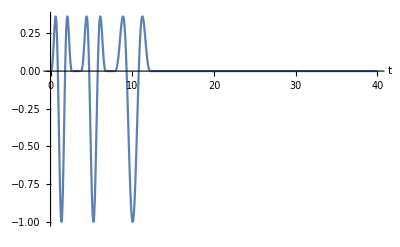

```mathematica
r=calcLengths[34,3,1.0]
periods=Array[r[[1,#]]/(√((r[[1,#]]g)/(2π)Tanh[(2π h)/r[[1,#]]]))&,Length[r[[1]]]]
Array[wavePeriod[r[[1,#]]]&,Length[r[[1]]]]
Array[travelTime[r[[1,#]]]+r[[2,#]]&,Length[r[[1]]]]

func=composeBoundary[r]
Plot[func,{time,0,40},AxesLabel->{"t"},PlotRange->All]
```

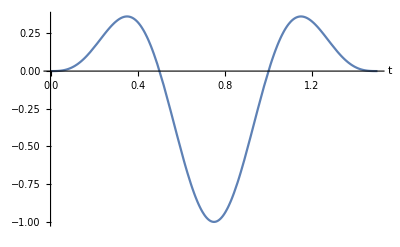

```mathematica
Plot[{
Sin[2π(x-r[[2,1]])]hanWindow[x,1.5],
},{x,0,1.5},AxesLabel->{"t"}]
```

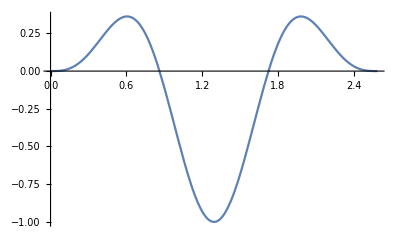

```mathematica
Plot[Sin[(2π)/periods[[1]](t-r[[2,1]])]hanWindow[t-r[[2,1]],1.5periods[[1]]],{t,0,1.5periods[[1]]}]
```